## NEGF

```mathematica
L=50;
a=1;L1=L;L2=L;
a1=a/2{3,√3,0};
a2=a/2{3,-√3,0};
b1={a,0,0};
uc = {0*b1,b1};
latt=Flatten[Table[n1*a1+n2*a2+u,{n1,L1},{n2,L2},{u,uc}],2];
dimH = Length[latt]
```

5000

```mathematica
dist[n1_,n2_]:=Norm[N[n2-n1]];
dists=Outer[dist,latt,latt,1];
```

```mathematica
Dimensions[dists]
```

{5000,5000}

```mathematica
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
```

```mathematica
neighbors=Position[dists,#,2]&/@ddists[[;;3]];
```

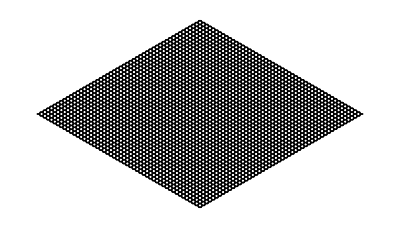

```mathematica
Graphics[{{{Black,CapForm["Butt"],Line[{latt[[#[[1]],1;;2]],latt[[#[[2]],1;;2]]}]}&/@neighbors[[2]]},{Black,Disk[#[[1;;2]],0.3]}&/@latt},ViewPoint->Top]
(*Graphics3D[{{{Black,CapForm["Butt"],Tube[{latt[[#[[1]]]],latt[[#[[2]]]]},.1]}&/@neighbors[[2]]},{Black,Sphere[#,0.3]}&/@latt},ViewPoint->Top];*)
```

SparseArray[…]

Eigensystem::arh: Because finding 5000 out of the 5000 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

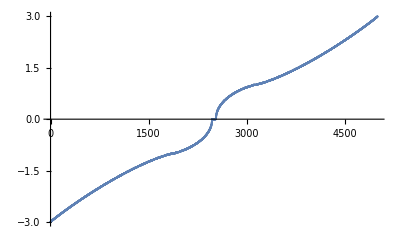

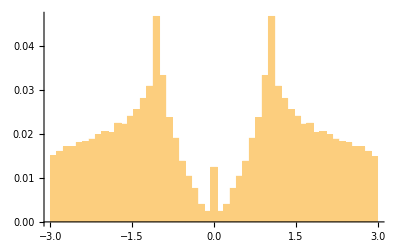

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];
H = SparseArray[#-> 1.0&/@neighbors[[2]]]
{energies,wavefunctions}=orderedEigensystem[H]//Sort;
ListPlot[energies]
max=Max[energies];min=Min[energies];
Histogram[energies,{min,max,(max-min)/51},"Probability"]
```

```mathematica
η=1*^-1;
Gs={};
Monitor[
Do[
AppendTo[Gs,{Inverse[N[ee*IdentityMatrix[Dimensions[H]]-H-ⅈ η IdentityMatrix[Dimensions[H]]]]}];
,{ee,ees}],ee]
```

```mathematica
η=1*^-1;
ees=Range[-4,4,0.1];
Gs=Inverse[N[#*IdentityMatrix[Dimensions[H]]-H-ⅈ η IdentityMatrix[Dimensions[H]]]]&/@ees;
```

```mathematica
As=Plus@@Re[Diagonal[-ⅈ*(#-#†)]]&/@Gs;
As/=Plus@@As
```

{0.000418053,0.00046551,0.000523569,0.000596219,0.000689766,0.000814819,0.000990723,0.00125682,0.00170623,0.00260932,0.0048173,0.00835082,0.010642,0.012319,0.0129549,0.0142941,0.0144032,0.0156777,0.015726,0.0163902,0.0174094,0.0177082,0.0182074,0.0196655,0.0197341,0.021207,0.0223849,0.0234304,0.0263058,0.0269936,0.0284785,0.0221759,0.0185536,0.015035,0.0117248,0.010389,0.00809896,0.00724081,0.00816572,0.0122185,0.0184529,0.0122185,0.00816572,0.00724081,0.00809896,0.010389,0.0117248,0.015035,0.0185536,0.0221759,0.0284785,0.0269936,0.0263058,0.0234304,0.0223849,0.021207,0.0197341,0.0196655,0.0182074,0.0177082,0.0174094,0.0163902,0.015726,0.0156777,0.0144032,0.0142941,0.0129549,0.012319,0.010642,0.00835082,0.0048173,0.00260932,0.00170623,0.00125682,0.000990723,0.000814819,0.000689766,0.000596219,0.000523569,0.00046551,0.000418053}

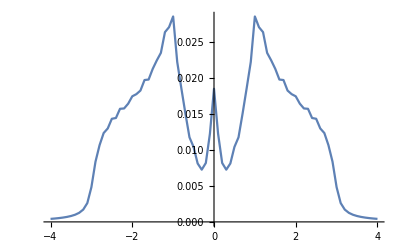

```mathematica
ListPlot[{ees,As}ᵀ,Joined->True,PlotRange->Full]
```